```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
a=0.4;
b=0.3;
c={0.5,0.5};
d=0.1;
```

```mathematica
y[s_]:=c+{a Cos[2 π s]/(2+Cos[2 π s]),b Sin[2π s]}
```

```mathematica
tabys=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/curvature/discontinuous/solution/y_s.csv"];
tabys=Table[{tabys[[i,2]],tabys[[i,3]]},{i,2,Length[tabys]}]
```

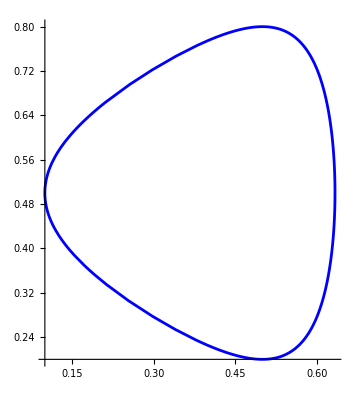

```mathematica
plotys=ParametricPlot[y[s],{s,0,1},PlotStyle->{Blue}]
```

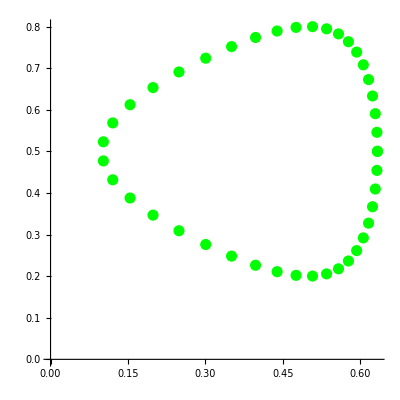

```mathematica
plotf=ListPlot[tabys,PlotStyle->{Green,PointSize->0.02,Opacity->1},AspectRatio->1]
```

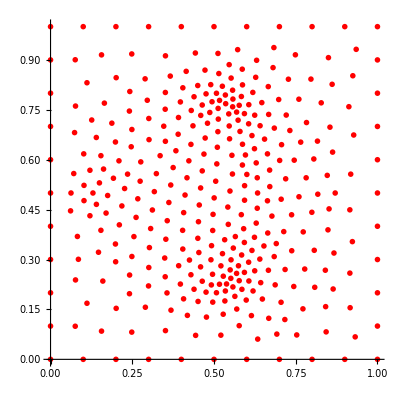

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/shape_line/solution/mesh_0/vertices.csv"];
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
plotve=ListPlot[tabve,PlotStyle->{Red,PointSize->0.01},AspectRatio->1]
```

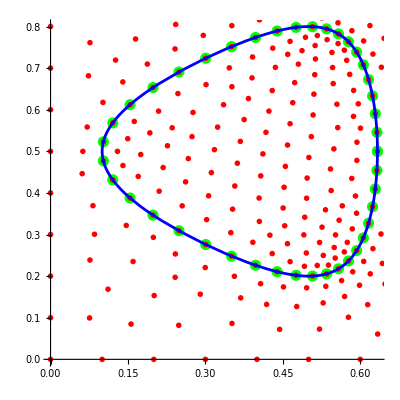

```mathematica
Show[plotf,plotve,plotys]
```